# plot gaussian and lorentzian

## for starters, anyhow. more comparisons to come.

## import data

```mathematica
basePath="C:/Users/Public/Documents/emma/udw-detector-shape/Cosine Trap Switching/";
```

```mathematica
dataNoCutoffG=Import[FileNameJoin[{basePath,"dataNoCutoffG.csv"}]];
dataSharpCutoffG=Import[FileNameJoin[{basePath,"dataSharpCutoffG.csv"}]];
dataExpCutoffG=Import[FileNameJoin[{basePath,"dataExpCutoffG.csv"}]];
```

```mathematica
dataNoCutoffL=Import[FileNameJoin[{basePath,"dataNoCutoffL.csv"}]];
dataSharpCutoffL=Import[FileNameJoin[{basePath,"dataSharpCutoffL.csv"}]];
dataExpCutoffL=Import[FileNameJoin[{basePath,"dataExpCutoffL.csv"}]];
```

```mathematica
psharpL10σ=Import[FileNameJoin[{basePath,"SharpL10Sig.csv"}]]
pexpL10σ=Import[FileNameJoin[{basePath,"ExpL10Sig.csv"}]]
```

{{0.995456}}

{{0.996418}}

```mathematica
psharpG10σ=Import[FileNameJoin[{basePath,"SharpG10Sig.csv"}]]
pexpG10σ=Import[FileNameJoin[{basePath,"ExpG10Sig.csv"}]]
```

{{0.995441}}

{{0.995413}}

```mathematica
σ
```

σ

## plot things

### plot data straight up

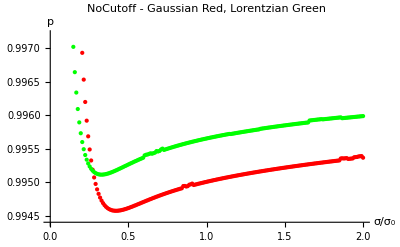

```mathematica
ListPlot[{dataNoCutoffG,dataNoCutoffL},
AxesLabel->{σ/Subscript[σ, 0],p},
PlotStyle->{Red,Green,Blue,Black},
PlotLabel->Style["NoCutoff - Gaussian Red, Lorentzian Green",FontSize->16]]
```

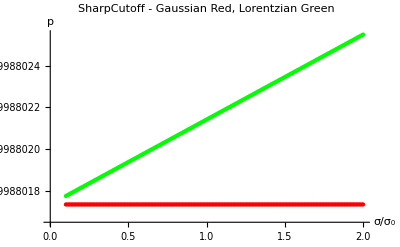

```mathematica
ListPlot[{dataSharpCutoffG,dataSharpCutoffL},
AxesLabel->{σ/Subscript[σ, 0],p},
PlotStyle->{Red,Green,Blue,Black},
PlotLabel->Style["SharpCutoff - Gaussian Red, Lorentzian Green",FontSize->16]]
```

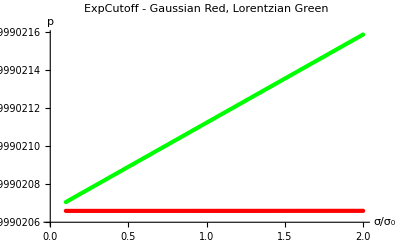

```mathematica
ListPlot[{dataExpCutoffG,dataExpCutoffL},
AxesLabel->{σ/Subscript[σ, 0],p},
PlotStyle->{Red,Green,Blue,Black},
PlotLabel->Style["ExpCutoff - Gaussian Red, Lorentzian Green",FontSize->16]]
```

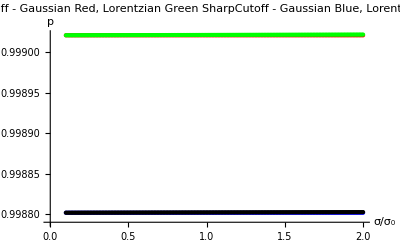

```mathematica
ListPlot[{dataExpCutoffG,dataExpCutoffL,dataSharpCutoffG,dataSharpCutoffL},
AxesLabel->{σ/Subscript[σ, 0],p},
PlotStyle->{Red,Green,Blue,Black},
PlotLabel->Style["ExpCutoff - Gaussian Red, Lorentzian Green\n SharpCutoff - Gaussian Blue, Lorentzian Black",FontSize->16]]
```

### plot percentage differences

```mathematica
pExpG=dataExpCutoffG[[All,2]];
pExpL=dataExpCutoffL[[All,2]];
pSharpG=dataSharpCutoffG[[All,2]];
pSharpL=dataSharpCutoffL[[All,2]];
```

```mathematica
σNormValues=dataExpCutoffG[[All,1]];
```

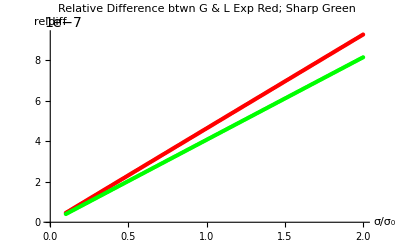

```mathematica
ListPlot[{Transpose[{σNormValues,Abs[pExpG-pExpL]/pExpG}],Transpose[{σNormValues,Abs[pSharpG-pSharpL]/pSharpG}]},
AxesLabel->{σ/Subscript[σ, 0],reldiff},
PlotStyle->{Red,Green,Blue,Black},
PlotLabel->Style["Relative Difference btwn G & L\n Exp Red; Sharp Green",FontSize->16]]
```

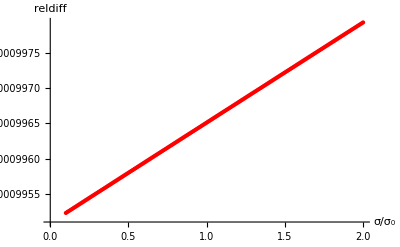

```mathematica
ListPlot[{Transpose[{σNormValues,Abs[pExpG-pExpL]/pExpG}]},
AxesLabel->{σ/Subscript[σ, 0],reldiff},
PlotStyle->{Red},
PlotLabel->Style["",FontSize->16]]
```

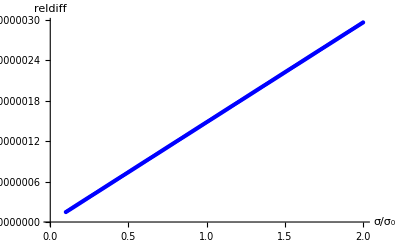

```mathematica
ListPlot[{Transpose[{σNormValues,Abs[pSharpG-pSharpL]/pSharpG}]},
AxesLabel->{σ/Subscript[σ, 0],reldiff},
PlotStyle->{Blue},
PlotLabel->Style["",FontSize->16]]
```

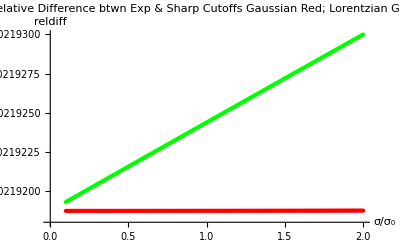

```mathematica
ListPlot[{Transpose[{σNormValues,Abs[pExpG-pSharpG]/pSharpG}],Transpose[{σNormValues,Abs[pExpL-pSharpL]/pSharpL}]},
AxesLabel->{σ/Subscript[σ, 0],reldiff},
PlotStyle->{Red,Green,Blue,Black},
PlotLabel->Style["Relative Difference btwn Exp & Sharp Cutoffs\n Gaussian Red; Lorentzian Green",FontSize->16]]
```

### conclusion from this data: the cutoff has a much greater affect on the transition probability than the smearing function at scales of the order of σ_0

### conclusion from previous data: the smearing function has a much greater affect on the transition probability than the cutoff at scales of the order 10^4 σ_0

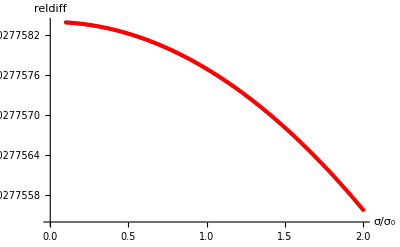

```mathematica
ListPlot[{Transpose[{σNormValues,Abs[pExpG-pSharpG]/pSharpG}]},
AxesLabel->{σ/Subscript[σ, 0],reldiff},
PlotStyle->{Red},
PlotLabel->Style["",FontSize->16]]
```

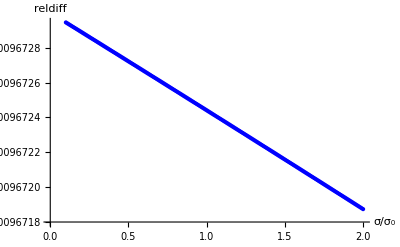

```mathematica
ListPlot[{Transpose[{σNormValues,Abs[pExpL-pSharpL]/pSharpL}]},
AxesLabel->{σ/Subscript[σ, 0],reldiff},
PlotStyle->{Blue},
PlotLabel->Style["",FontSize->16]]
```

### plot relative difference as compared to P_δ

```mathematica
λ=0.1;
psharpδ=1-0.11982647992551805 λ^2
pexpδ=1-0.09793401746569944 λ^2
```

0.998802

0.999021

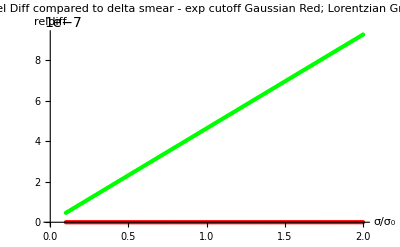

```mathematica
ListPlot[{Transpose[{σNormValues,Abs[pExpG-pexpδ]/pexpδ}],Transpose[{σNormValues,Abs[pExpL-pexpδ]/pexpδ}]},
AxesLabel->{σ/Subscript[σ, 0],reldiff},
PlotStyle->{Red,Green,Blue,Black},
PlotLabel->Style["Rel Diff compared to delta smear - exp cutoff\n Gaussian Red; Lorentzian Green",FontSize->16]]
```

#### teeny!

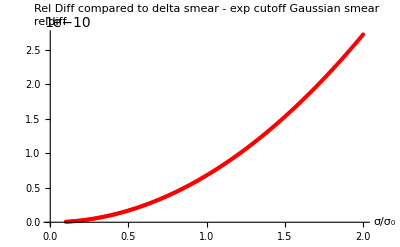

```mathematica
ListPlot[{Transpose[{σNormValues,Abs[pExpG-pexpδ]/pexpδ}]},
AxesLabel->{σ/Subscript[σ, 0],reldiff},
PlotStyle->{Red},
PlotLabel->Style["Rel Diff compared to delta smear - exp cutoff\n Gaussian smear",FontSize->16]]
```

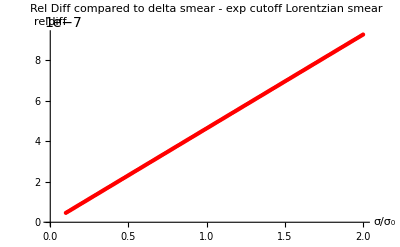

```mathematica
ListPlot[{Transpose[{σNormValues,Abs[pExpL-pexpδ]/pexpδ}]},
AxesLabel->{σ/Subscript[σ, 0],reldiff},
PlotStyle->{Red},
PlotLabel->Style["Rel Diff compared to delta smear - exp cutoff\n Lorentzian smear",FontSize->16]]
```

#### a gaussian smearing is much closer to a delta smear than lorentzian is ---intuitively, this makes sense, as a delta is a limit of a gaussian

## relative difference for different σ, fixed cutoff & smearing

```mathematica
σNormValues[[1]]
```

0.1

```mathematica
σNormValues[[201]]
```

2.

### gaussian smear, sharp cutoff

```mathematica
Abs[pSharpG[[201]]-pSharpG[[1]]]/pSharpG[[1]]
```

9.55566×10^-11

```mathematica
Abs[psharpG10σ-pSharpG[[1]]]/pSharpG[[1]]
```

{{2.39466×10^-9}}

### gaussian smear, exp cutoff

```mathematica
Abs[pExpG[[201]]-pExpG[[1]]]/pExpG[[1]]
```

2.71084×10^-10

```mathematica
Abs[pexpG10σ-pExpG[[1]]]/pExpG[[1]]
```

{{6.79313×10^-9}}

### lorentzian smear, sharp cutoff

```mathematica
Abs[pSharpL[[201]]-pSharpL[[1]]]/pSharpL[[1]]
```

7.73983×10^-7

```mathematica
Abs[psharpL10σ-pSharpL[[1]]]/pSharpL[[1]]
```

{{4.02529×10^-6}}

### lorentzian smear, exp cutoff

```mathematica
Abs[pExpL[[201]]-pExpL[[1]]]/pExpL[[1]]
```

8.80917×10^-7

```mathematica
Abs[pexpL10σ-pExpL[[1]]]/pExpL[[1]]
```

{{4.56871×10^-6}}